```mathematica
Export["test.gif",Plot[Sin[x],{x,0,10}]]
```

test.gif

## Spherically symmetric case (1+1D nonlinear PDE)

As in the draft eq. (4.61), I write ∂lnH/∂lna as

```mathematica
dlnHdlna = -(Ωm + (1+3w)(1-Ωm)Exp[-3w lna])/(2Ωm + 2(1-Ωm)Exp[-3w lna]);
```

As an example I will put “nice” numbers, Ωm = 3/10 and w = -5/6. We can solve the time evolution of the linear gravitational potential ψ:

```mathematica
DSolve[(ψ''[lna] +(3+dlnHdlna)ψ'[lna]+(2-(3Ωm)/(2Ωm + 2(1-Ωm)Exp[-3w lna])+dlnHdlna)ψ[lna]== 0)/.Ωm-> 3/10/.w-> -5/6,ψ[lna], lna]
```

{{ψ[lna]→C[1] Hypergeometric2F1[2/5,11/10,2,-7/3 ⅇ^(5 lna/2)]+C[2] MeijerG[{{},{-1/10,3/5}},{{-1,0},{}},-7/3 ⅇ^(5 lna/2)]}}

The first solution is the relevant one (it becomes constant as lna -> -∞):

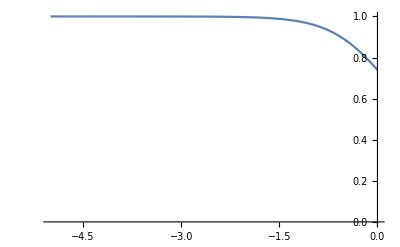

```mathematica
Plot[Hypergeometric2F1[2/5,11/10,2,-7/3 ⅇ^(5 lna/2)],{lna,-5,0},PlotRange->{0,1}]
```

```mathematica
Hypergeometric2F1[2/5,11/10,2,-7/3 ⅇ^(5 lna/2)]/.lna->0.0001//N
```

0.739243

```mathematica
MeijerG[{{},{-1/10,3/5}},{{-1,0},{}},-7/3 ⅇ^(5 lna/2)]/.lna->-2//N
```

-66.8459-0.196734 ⅈ

```mathematica
Hypergeometric2F1[2/5,11/10,2,-7/3 ⅇ^(5 lna/2)]
```

Hypergeometric2F1[2/5,11/10,2,-7/3 ⅇ^(5 lna/2)]

We now need to choose the radial profile of ψ. As is well known, every spherically symmetric function can be expanded in terms of j_0(k r). Let us consider a single spherical wave mode with wave number k. Note that in the following k and r will use units of H_0 so that everything is dimensionless.

```mathematica
ψ[lna_,r_]:= amplitude Hypergeometric2F1[2/5,11/10,2,-7/3 ⅇ^(5 lna/2)] SphericalBesselJ[0,k r];
```

Let me call π̃ of eq. (4.59) “p[lna,r]”. This will take a while (a few minutes on my laptop) - I have already dialled the parameter values to something vaguely workable.

```mathematica
nsol =NDSolve[{(Derivative[2,0][p][lna,r] + (1-3w-dlnHdlna)Derivative[1,0][p][lna,r]+(3w(dlnHdlna-1)-D[dlnHdlna,lna])p[lna,r]+3w ψ[lna,r]-D[ψ[lna,r],lna] ==(2-3w)/(2(Ωm Exp[-lna]+(1-Ωm)Exp[-(1+3w)lna]))(Derivative[0,1][p][lna,r])^2)/.Ωm-> 3/10/.w-> -5/6,p[-8,r] == 0,Derivative[1,0][p][-8,r]== ψ[-8,r]/2}/.amplitude-> -2/100/.k-> 20,p,{lna, -7.5,-0.75},{r,-2,2},MaxStepSize-> 0.02]
```

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable r. Artificial boundary effects may be present in the solution.

{{p→InterpolatingFunction[{{-7.5, -0.75}, {-2., 2.}}, <>]}}

```mathematica
(*scalarfield = Table[p[lna,r] /√(Ωm Exp[-lna]+(1-Ωm)Exp[-(1+3w)lna])/.Ωm-> 3/10/.w-> -5/6/.nsol,{lna,-2,-2}];*)
```

```mathematica
(*Dxscalarfield = Table[Derivative[0,1][p][lna,r] /√(Ωm Exp[-lna]+(1-Ωm)Exp[-(1+3w)lna])/.Ωm-> 3/10/.w-> -5/6/.nsol,{lna,-2,-9/10,1/10}]*)
```

```mathematica
redshift[lna_] :=1/Exp[lna]-1;
```

```mathematica
redshift[-0.9]//N
```

1.4596

```mathematica
A0[r_]:=p[lna,r] /√(Ωm Exp[-lna]+(1-Ωm)Exp[-(1+3w)lna])/.Ωm-> 3/10/.w-> -5/6/.lna->-3.045/.nsol(*z=20*)
A1[r_]:=p[lna,r] /√(Ωm Exp[-lna]+(1-Ωm)Exp[-(1+3w)lna])/.Ωm-> 3/10/.w-> -5/6/.lna->-2.4/.nsol(*z=10*)
A2[r_]:=p[lna,r] /√(Ωm Exp[-lna]+(1-Ωm)Exp[-(1+3w)lna])/.Ωm-> 3/10/.w-> -5/6/.lna->-1.948/.nsol(*z=6*)
A3[r_]:=p[lna,r] /√(Ωm Exp[-lna]+(1-Ωm)Exp[-(1+3w)lna])/.Ωm-> 3/10/.w-> -5/6/.lna->-1.39/.nsol(*z=3*)
A4[r_]:=p[lna,r] /√(Ωm Exp[-lna]+(1-Ωm)Exp[-(1+3w)lna])/.Ωm-> 3/10/.w-> -5/6/.lna->-0.9/.nsol(*z=1.45*)
```

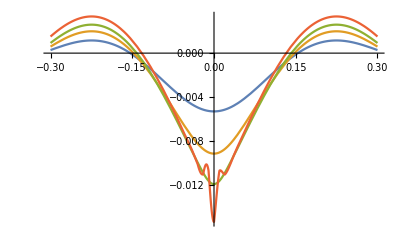

```mathematica
Plot[{A0[r],A2[r],A3[r],A4[r]},{r,-0.3,0.3}]
```

```mathematica
(*A[r]*)
```

```mathematica
(*data = Table[{r,A[r]},{r,-0.3,0.3,0.01}];*)
```

```mathematica
(*if=Interpolation[data]
*)
```

```mathematica
(*pw[u_]:=Piecewise[{{{A0[u],A[u]},u<0.5},{{A0[u],0.5},u≥0.5}}]*)

p1 =RevolutionPlot3D[{A0[u][[1]]},{u,-0.7,0.7},{x,-1.8,1.8},PlotRange->{-0.013,0.006},Mesh->None,ImageSize->Large,AspectRatio->0.9,ViewPoint->{3.5,2.5,0.5},PlotStyle->Opacity[0.9],ColorFunction->"TemperatureMap",Boxed->False,Axes->{False,False,False},PlotLabels->Style["z=20",FontSize->25],ColorFunctionScaling->True]
(*p2=RevolutionPlot3D[{A1[u][[1]]},{u,-0.7,0.7},{x,-1.8,1.8},PlotRange->{-0.02,0.006},Mesh->Full,ImageSize->Large,AspectRatio->0.9,ViewPoint->{3.5,2.5,0.5},PlotStyle->Opacity[0.9],LabelStyle->"z=10",ColorFunction->"TemperatureMap",Boxed->False,Axes->False,PlotLabels->Style["z=10",FontSize->25]]*)
p3=RevolutionPlot3D[{A2[u][[1]]},{u,-0.7,0.7},{x,-1.8,1.8},PlotRange->{-0.013,0.006},Mesh->None,ImageSize->Large,AspectRatio->0.9,ViewPoint->{3.5,2.5,0.5},PlotStyle->Opacity[0.9],ColorFunction->"TemperatureMap",Boxed->False,Axes->{False,False,False},PlotLabels->Style["z=6",FontSize->25]]
(*p4=RevolutionPlot3D[{A3[u][[1]]},{u,-0.7,0.7},{x,-1.8,1.8},PlotRange->{-0.013,0.006},Mesh->None,ImageSize->Large,AspectRatio->0.9,ViewPoint->{3.5,2.5,0.5},PlotStyle->Opacity[0.9],ColorFunction->"TemperatureMap",Boxed->False,Axes->False,PlotLabels->Style["z=3",FontSize->25]]*)
p5=RevolutionPlot3D[{A4[u][[1]]},{u,-0.7,0.7},{x,-1.8,1.8},PlotRange->{-0.013,0.006},Mesh->None,ImageSize->Large,AspectRatio->0.9,ViewPoint->{3.5,2.5,0.5},PlotStyle->Opacity[0.9],ColorFunction->"TemperatureMap",Boxed->False,Axes->{False,False,True},AxesStyle->Thick,TicksStyle->Large,PlotLabels->Style["z=1.45",FontSize->25]]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
p5=RevolutionPlot3D[{A4[u][[1]]},{u,-0.7,0.7},{x,-1.8,1.8},PlotRange->{-0.02,0.005},Mesh->None,ImageSize->Large,AspectRatio->0.9,ViewPoint->{3.5,2.5,0.5},PlotStyle->Opacity[0.9],ColorFunction->"TemperatureMap",Boxed->False,Axes->True,PlotLabels->Style["z=1.11",FontSize->25],PlotLabels->Placed["z=1.11",Above],LabelingSize->Full]
```

-Graphics3D-

```mathematica
p4=RevolutionPlot3D[{A1[u][[1]]},{u,-0.7,0.7},{x,-1.8,1.8},PlotRange->{-0.02,0.006},Mesh->Full,ImageSize->Large,AspectRatio->0.9,ViewPoint->{3.5,2.5,0.5},PlotStyle->Opacity[0.9],LabelStyle->"z=20",ColorFunction->"LakeColors",Boxed->False,Axes->False,PlotLabels->Style["z=20",FontSize->25]]
```

-Graphics3D-

-Graphics3D-

```mathematica
Show[{p1,p3},PlotRange->{-0.013,0.005},Epilog->{Inset[Framed[Style["Top Right",20],Background->White],{45,2300}],Inset[Framed[Style["Bottom Right",20],Background->White],{45,300}]}]
```

RevolutionPlot3D::nonopt: Options expected (instead of z=20) beyond position 3 in RevolutionPlot3D[{A0[u]⟦1⟧},{u,-0.7,0.7},{x,-1.8,1.8},PlotRange→{-0.02,0.006},Mesh→Full,ImageSize→Large,AspectRatio→0.9,ViewPoint→{3,2,0.4},PlotStyle→Opacity[0.9],LabelStyle→z=20,ColorFunction→LakeColors,Boxed→False,Axes→False,z=20]. An option must be a rule or a list of rules.

Show::gcomb: Could not combine the graphics objects in ….

Show[{RevolutionPlot3D[{A0[u]⟦1⟧},{u,-0.7,0.7},{x,-1.8,1.8},PlotRange→{-0.02,0.006},Mesh→Full,ImageSize→Large,AspectRatio→0.9,ViewPoint→{3,2,0.4},PlotStyle→Opacity[0.9],LabelStyle→z=20,ColorFunction→LakeColors,Boxed→False,Axes→False,z=20{2.5,Above}],-Graphics3D-},PlotRange→{-0.013,0.005},Epilog→{Inset[Top Right,{45,2300}],Inset[Bottom Right,{45,300}]}]

Let us finally look at π(lna,r) itself (remember that π̃ was a rescaled quantity). One can see that a spike forms at the centre quite suddenly.

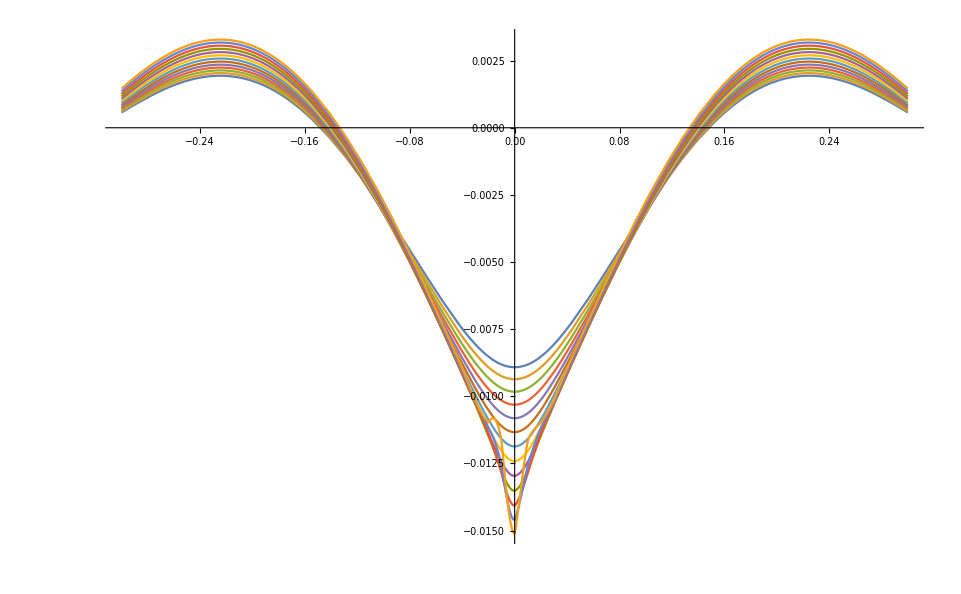

```mathematica
Plot[scalarfield,{r,-0.3,0.3}]
```

```mathematica
(*Plot[Table[Derivative[0,1][p][lna,r] /√(Ωm Exp[-lna]+(1-Ωm)Exp[-(1+3w)lna])/.Ωm-> 3/10/.w-> -5/6/.nsol,{lna,-2,-9/10,1/10}],{r,-0.3,0.3}]*)
```

```mathematica
ArrayPatternMesh[a_?ArrayQ]:=Module[{mp,pos,fpos,dims=Dimensions[a],cdims},mp=RegionProduct@@Map[MeshRegion[Partition[N[Range[0,#]]/#,1],Line[Range[1,#+1]]]&,dims];
pos=ArrayRules[a][[1;;-2,1]];
cdims=Reverse[FoldList[Times,1,dims[[2;;-1]]]];
fpos=1+(pos-1).cdims;
MeshRegion[MeshCoordinates[mp],MeshCells[mp,{Length[dims],fpos}]]];
drill[s_,t_]:=Block[{sp,d=ArrayDepth[t],r=Length[s]/Length[t]},If[r==1,Mod[t s,2],sp=Partition[s,Dimensions[s]/Dimensions[t]];
Flatten[MapThread[If[#1==0,#2 0,drill[#2,t]]&,{t,sp},d],Transpose[Partition[Range[2 d],d]]]]];
SierpinskiArray[t_,k_]:=Module[{s,dims=Dimensions[t]},s=ConstantArray[1,dims^k];
drill[s,t]];
```

```mathematica
t={{{1,1,1},{1,0,1},{1,1,1}},{{1,0,1},{0,0,0},{1,0,1}},{{1,1,1},{1,0,1},{1,1,1}}};
mr=ArrayPatternMesh[SierpinskiArray[t,3]]
```

-Graphics3D-